# Hall MHD phase and group diagram

## Analytic expression from Vocks, Motschmann and Glassmeier 1999

```mathematica
ω[Psi_,va_,c0_]:=Table[(k d)/va √(X1/3+2/3 √-a Cos[1/3 ArcTan[√(-1-(4 a^3)/b^2)]+(2m)/3 π]),{m,0,2,1}]
```

```mathematica
X1=c0^2+va^2+Cos[Psi]^2 va^2+Cos[Psi]^2 d^2 k^2 va^2;
X2=2 c0^2+c0^2 d^2 k^2+va^2;
a=-X1^2+3 Cos[Psi]^2 va^2 X2;
b=27 Cos[Psi]^4 c0^2 va^4+2 X1^3-9 Cos[Psi]^2 va^2 X1 X2;
d=va/Subscript[Ω, i];
```

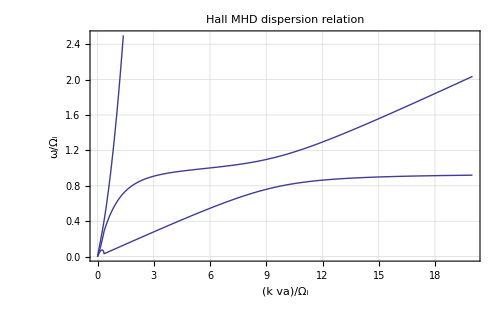

```mathematica
Plot[ω[Psi,va,c0]/.{va->1,c0->0.1,Subscript[Ω, i]->1,Psi->20π/180},{k,0,20},
PlotRange->{{0,20},{0,2.5}},
ImageSize->500,GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,FrameLabel->{k d,ω/Subscript[Ω, i]},PlotLabel->"Hall MHD dispersion relation"]
```

Phase velocities

```mathematica
Manipulate[
PolarPlot[ω[Psi,va,c0]/k/.{va->0.96824,c0->1.29099,k->K,Subscript[Ω, i]->1},{Psi,-π,π},
AspectRatio->1,Frame->True,
FrameLabel->{Subscript[v, z]/Subscript[Ω, i],Subscript[v, x]/Subscript[Ω, i]},
PlotLabel->"Hall MHD Phase velocities, k*d="<>ToString[K],
ImageSize->{{400}},PlotRangePadding->None,PlotRange->All],
{K,0.0,20}]
```

Group velocities

```mathematica
vgt[Psi_,va_,c0_]=D[ω[Psi,va,c0],Psi]/k*Subscript[Ω, i];
vgk[Psi_,va_,c0_]=D[ω[Psi,va,c0],k]*Subscript[Ω, i];
```

```mathematica
Manipulate[
myva=0.96824;
myc0=1.29099;
myΩi=100*myva;
range={{-4,4},{-4,4}};
Show[
ParametricPlot[{Cos[Psi]vgk[Psi,va,c0]⟦1⟧-Sin[Psi]vgt[Psi,va,c0]⟦1⟧,Sin[Psi]vgk[Psi,va,c0]⟦1⟧+Cos[Psi]vgt[Psi,va,c0]⟦1⟧}/.{va->myva,c0->myc0,Subscript[Ω, i]->myΩi,k->K },{Psi,-π,π},
AspectRatio->Automatic,
PlotRange->All,
Frame->True,
PlotStyle->{{Green}},
FrameLabel->{Subscript[v, z],Subscript[v, x]},
PlotLabel->"Hall MHD Group velocities, k="<>ToString[K],
ImageSize->{{400}},PlotRangePadding->None,PlotRange->All],

ParametricPlot[{Cos[Psi]vgk[Psi,va,c0]⟦2⟧-Sin[Psi]vgt[Psi,va,c0]⟦2⟧,Sin[Psi]vgk[Psi,va,c0]⟦2⟧+Cos[Psi]vgt[Psi,va,c0]⟦2⟧}/.{va->myva,c0->myc0,Subscript[Ω, i]->myΩi,k->K },{Psi,-π,π},
AspectRatio->Automatic,Frame->True,
PlotStyle->{{Red}},
FrameLabel->{Subscript[v, z],Subscript[v, x]},
PlotLabel->"Hall MHD Group velocities, k="<>ToString[K],
ImageSize->{{400}},PlotRangePadding->None,PlotRange->All],

ParametricPlot[{Cos[Psi]vgk[Psi,va,c0]⟦3⟧-Sin[Psi]vgt[Psi,va,c0]⟦3⟧,Sin[Psi]vgk[Psi,va,c0]⟦3⟧+Cos[Psi]vgt[Psi,va,c0]⟦3⟧}/.{va->myva,c0->myc0,Subscript[Ω, i]->myΩi,k->K },{Psi,-π,π},
AspectRatio->Automatic,Frame->True,
PlotStyle->{{Blue}},
FrameLabel->{Subscript[v, z],Subscript[v, x]},
PlotLabel->"Hall MHD Group velocities, k="<>ToString[K],
ImageSize->{{400}},PlotRangePadding->None,PlotRange->All]
]
,{K,0,3000}]
```

```mathematica
vgt[Psi,va,c0]
```

{((Sin[1/3 ArcTan[√(-1-(4 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)/((27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2))]] (-(12 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^2 (-6 va^2 Cos[Psi] Sin[Psi] (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2) (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2)))/(27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2+(8 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3 (-108 c0^2 va^4 Cos[Psi]^3 Sin[Psi]+18 va^2 Cos[Psi] Sin[Psi] (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2)+6 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2 (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2)))/(27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^3) √(-3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)+(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2) (27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2)/(36 √(-1-(4 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)/((27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2)) (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)+(Cos[1/3 ArcTan[√(-1-(4 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)/((27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2))]] (6 va^2 Cos[Psi] Sin[Psi] (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2) (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2)))/(3 √(-3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)+(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2))+1/3 (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2))/(2 √(2/3 Cos[1/3 ArcTan[√(-1-(4 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)/((27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2))]] √(-3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)+(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)+1/3 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2))),((Cos[π/6+1/3 ArcTan[√(-1-(4 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)/((27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2))]] (-(12 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^2 (-6 va^2 Cos[Psi] Sin[Psi] (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2) (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2)))/(27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2+(8 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3 (-108 c0^2 va^4 Cos[Psi]^3 Sin[Psi]+18 va^2 Cos[Psi] Sin[Psi] (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2)+6 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2 (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2)))/(27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^3) √(-3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)+(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2) (27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2)/(36 √(-1-(4 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)/((27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2)) (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)-(Sin[π/6+1/3 ArcTan[√(-1-(4 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)/((27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2))]] (6 va^2 Cos[Psi] Sin[Psi] (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2) (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2)))/(3 √(-3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)+(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2))+1/3 (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2))/(2 √(-2/3 Sin[π/6+1/3 ArcTan[√(-1-(4 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)/((27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2))]] √(-3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)+(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)+1/3 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2))),(-(Cos[π/6-1/3 ArcTan[√(-1-(4 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)/((27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2))]] (-(12 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^2 (-6 va^2 Cos[Psi] Sin[Psi] (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2) (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2)))/(27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2+(8 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3 (-108 c0^2 va^4 Cos[Psi]^3 Sin[Psi]+18 va^2 Cos[Psi] Sin[Psi] (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2)+6 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2 (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2)))/(27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^3) √(-3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)+(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2) (27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2)/(36 √(-1-(4 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)/((27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2)) (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)-(Sin[π/6-1/3 ArcTan[√(-1-(4 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)/((27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2))]] (6 va^2 Cos[Psi] Sin[Psi] (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2) (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2)))/(3 √(-3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)+(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2))+1/3 (-2 va^2 Cos[Psi] Sin[Psi]-(2 k^2 va^4 Cos[Psi] Sin[Psi])/Ω_i^2))/(2 √(-2/3 Sin[π/6-1/3 ArcTan[√(-1-(4 (3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)-(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)^3)/((27 c0^2 va^4 Cos[Psi]^4-9 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2) (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)+2 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^3)^2))]] √(-3 va^2 Cos[Psi]^2 (2 c0^2+va^2+(c0^2 k^2 va^2)/Ω_i^2)+(c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)^2)+1/3 (c0^2+va^2+va^2 Cos[Psi]^2+(k^2 va^4 Cos[Psi]^2)/Ω_i^2)))}